```mathematica
Quit[];
```

```mathematica
(*******************************************************************************************)
(************************************** ACOPLAMIENTOS **************************************)
(*******************************************************************************************)
mτ=1.776.86; emτ=0.12*10^(-3);
mb=4.180; emb=40*10^(-3);
mc=1.270; emc=30*10^(-3);
mu=2.2*10^(-3); emu=0.6*10^(-3);
(*Vub=3.7*10^-3; eVub=0.39*10^-3;*)
mB=5.27931; emB=0.15*10^(-3);

Dd=DiagonalMatrix[{md,ms,mb}];
Du=DiagonalMatrix[{mu,mc,mt}];
Dl=DiagonalMatrix[{me,mμ,mτ}];
V={{Vud,Vus,Vub},{Vcd,Vcs,Vcb},{Vtd,Vts,Vtb}};
Vnum={{Cos[θ12]*Cos[θ13],Sin[θ12]*Cos[θ13],Sin[θ13]*Exp[-I*δ]},{-Sin[θ12]*Cos[θ23]-Sin[θ13]*Sin[θ23]*Cos[θ12]*Exp[I*δ],Cos[θ12]*Cos[θ23]-Sin[θ12]*Sin[θ23]*Sin[θ13]*Exp[I*δ],Sin[θ23]*Cos[θ13]},{Sin[θ12]*Sin[θ23]-Sin[θ13]*Cos[θ23]*Cos[θ12]*Exp[I*δ],-Cos[θ12]*Sin[θ23]-Sin[θ12]*Cos[θ23]*Sin[θ13]*Exp[I*δ],Cos[θ13]*Cos[θ23]}};
Upmns={{Ue1,Ue2,Ue3},{Uμ1,Uμ2,Uμ3},{Uτ1,Uτ2,Uτ3}};
UpmnsNum={{Cos[θl12]*Cos[θl13],Sin[θl12]*Cos[θl13],Sin[θl13]*Exp[-I*δl]},{-Sin[θl12]*Cos[θl23]-Sin[θl13]*Sin[θl23]*Cos[θl12]*Exp[I*δl],Cos[θl12]*Cos[θl23]-Sin[θl12]*Sin[θl23]*Sin[θl13]*Exp[I*δl],Sin[θl23]*Cos[θl13]},{Sin[θl12]*Sin[θl23]-Sin[θl13]*Cos[θl23]*Cos[θl12]*Exp[I*δl],-Cos[θl12]*Sin[θl23]-Sin[θl12]*Cos[θl23]*Sin[θl13]*Exp[I*δl],Cos[θl13]*Cos[θl23]}};
Upmns={{Ue1,Ue2,Ue3},{Uμ1,Uμ2,Uμ3},{Uτ1,Uτ2,Uτ3}};

(*** Angulos para calcular Upmns ***)
θl12=ArcSin[Sqrt[0.297]];
θl13=ArcSin[Sqrt[0.0241]];
θl23=ArcSin[Sqrt[0.437]];
δl=Pi*1.35;

(*** Angulos para calcular Vckm ***)
λ=0.22506;
A=0.811;
ρ=0.124;
η=0.356;
Aux=A*λ^3*(ρ+I*η);

θ12=ArcSin[λ];
θ13=ArcSin[Abs[Aux]];
θ23=ArcSin[A*λ^2];
δ=Arg[Aux];

Upmns=UpmnsNum;
V=Vnum;

(*** DEFINICION DEL MODELO ***)
nl1=Upmns[[1,3]];nl2=Upmns[[2,3]];nl3=Upmns[[3,3]]; (**SIN CONJUGATE nl1=Upmns[[1,3]];nl2=Upmns[[2,3]];nl3=Upmns[[3,3]];**)
(*n1=V[[1,3]];n2=V[[2,3]];n3=V[[3,3]]; (**SIN CONJUGATE**)
n1=0;n2=0;n3=1;*) 
U={{0,0,n1},{0,0,n2},{0,0,n3}};
Ul={{0,0,nl1},{0,0,nl2},{0,0,nl3}};
P=DiagonalMatrix[{0,0,1}];


Uτ1=Upmns[[3,1]];
Uτ2=Upmns[[3,2]];
Uτ3=Upmns[[3,3]];
```

# Calculo Acoplamientos

## B-lν

```mathematica
Nu=t*Du-(t+t^(-1))*U.P.ConjugateTranspose[U].Du;
VNd=t*V.Dd-(t+t^(-1))*U.P.ConjugateTranspose[U].V.Dd;
Nl=t*Dl-(t+t^(-1))*Ul.P.ConjugateTranspose[Ul].Dl;
UNl=(ConjugateTranspose[Upmns].Nl);

gRleptonic=-(VNd)[[1,3]]/(mτ*V[[1,3]]);
gLleptonic=(ConjugateTranspose[Nu].V)[[1,3]]/(mτ*V[[1,3]]);

gRleptonic=Simplify[gRleptonic,Element[{t,θ12,θ13,θ23,δ},Reals]];
gLleptonic=Simplify[gLleptonic,Element[{t,θ12,θ13,θ23,δ},Reals]];
 UNl=Simplify[UNl,Element[{t,θl12,θl13,θl23,δl},Reals]];


gRleptonic=gRleptonic*UNl;
gLleptonic=gLleptonic*UNl;



FormulaBlu=Simplify[Abs[Conjugate[Uτ1]-mB^2/(mH^2*(mu+mb))*(gRleptonic-gLleptonic)[[1,3]]]^2+Abs[Conjugate[Uτ2]-mB^2/(mH^2*(mu+mb))*(gRleptonic-gLleptonic)[[2,3]]]^2+Abs[Conjugate[Uτ3]-mB^2/(mH^2*(mu+mb))*(gRleptonic-gLleptonic)[[3,3]]]^2,Element[{mB,t,mH,mu,mb},Reals]];
```

## B-D[*]lν

```mathematica
Nu=t*Du-(t+t^(-1))*U.P.Transpose[U].Du;
VNd=t*V.Dd-(t+t^(-1))*U.P.ConjugateTranspose[U].V.Dd;
Nl=t*Dl-(t+t^(-1))*Ul.P.ConjugateTranspose[Ul].Dl;
UNl=(ConjugateTranspose[Upmns].Nl);

gR=-(VNd)[[2,3]]/(V[[2,3]]);
gL=(ConjugateTranspose[Nu].V)[[2,3]]/(V[[2,3]]);

gR=Simplify[gR,Element[{t,θ12,θ13,θ23,δ},Reals]];
gL=Simplify[gL,Element[{t,θ12,θ13,θ23,δ},Reals]];
 UNl=Simplify[UNl/ConjugateTranspose[Upmns],Element[{t,θl12,θl13,θl23,δl},Reals]];

(*gR=ReplaceAll[gR*UNl,{θ12->ArcSin[λ],θ23->ArcSin[A*λ^2],θ13->ArcSin[Abs[Aux]],δ->Arg[Aux],θl12->ArcSin[sinθl12],θl23->ArcSin[sinθl23],θl13->ArcSin[sinθl13],δl->deltal}];
gL=ReplaceAll[gL*UNl,{θ12->ArcSin[λ],θ23->ArcSin[A*λ^2],θ13->ArcSin[Abs[Aux]],δ->Arg[Aux],θl12->ArcSin[sinθl12],θl23->ArcSin[sinθl23],θl13->ArcSin[sinθl13],δl->deltal}];*)
gR=gR*UNl;
gL=gL*UNl;
```

### B-Dlν

```mathematica
FormulaBDlu=Simplify[1+Abs[Uτ1]^2*(1.5*Re[(gL+gR)[[1,3]]/(mH^2)]+1*(Abs[(gL+gR)[[1,3]]/(mH^2)])^2)+Abs[Uτ2]^2*(1.5*Re[(gL+gR)[[2,3]]/(mH^2)]+1*(Abs[(gL+gR)[[2,3]]/(mH^2)])^2)+Abs[Uτ3]^2*(1.5*Re[(gL+gR)[[3,3]]/(mH^2)]+1*(Abs[(gL+gR)[[3,3]]/(mH^2)])^2),Element[{mH,t,θl12,θl13,θl23,δl,mc,mb,mt,mu,mτ},Reals]];
```

### B-D*lν

```mathematica
FormulaBDslu=Simplify[(1+Abs[Uτ1]^2*(0.12*Re[(-gL+gR)[[1,3]]/(mH^2)]+0.05*(Abs[(-gL+gR)[[1,3]]/(mH^2)])^2)+Abs[Uτ2]^2*(0.12*Re[(-gL+gR)[[2,3]]/(mH^2)]+0.05*(Abs[(-gL+gR)[[2,3]]/(mH^2)])^2)+Abs[Uτ3]^2*(0.12*Re[(-gL+gR)[[3,3]]/(mH^2)]+0.05*(Abs[(-gL+gR)[[3,3]]/(mH^2)])^2)),Element[{mH,t,θl12,θl13,θl23,δl,mc,mb,mt,mu,mτ},Reals]];
```

### Parámetros del fit

```mathematica
(*** Valores B->lu ***)
Γexp=1.06*10^-4;eΓexp=0.2*10^-4;(*PDG 2016*)
Γteo=7.58*10^-5;eΓteo=0.8*10^-5;(*CKM Fitter*)
Blu=Γexp/Γteo;  eBlu=Blu*(eΓexp/Γexp+eΓteo/Γteo);

(*** Valores B->Dlu ***)
Rsm=0.299;eRsm=0.011;
Rdexp=0.407;eRdexp=0.039;(* http://www.slac.stanford.edu/xorg/hflav/semi/fpcp17/RDRDs.html *)
BDlu=Rdexp/Rsm;eBDlu=BDlu*(eRdexp/Rdexp+eRsm/Rsm);

(*** Valores B->D*lu ***)
Rsm=0.252;eRsm=0.003;(*1203.2654*)
Rdexp=0.304;eRdexp=0.013;  (* http://www.slac.stanford.edu/xorg/hflav/semi/fpcp17/RDRDs.html *)
BDslu=Rdexp/Rsm;eBDslu=BDslu*(eRdexp/Rdexp+eRsm/Rsm);


fBlu[mH_,t_,α_,β_]=Module[{n1=Sin[α]*Cos[β],n2=Sin[α]*Sin[β],n3=Cos[α]},Evaluate[FormulaBlu]];
fBDlu[mH_,t_,α_,β_]=Module[{n1=Sin[α]*Cos[β],n2=Sin[α]*Sin[β],n3=Cos[α]},Evaluate[FormulaBDlu]];
fBDslu[mH_,t_,α_,β_]=Module[{n1=Sin[α]*Cos[β],n2=Sin[α]*Sin[β],n3=Cos[α]},Evaluate[FormulaBDslu]];

(*** Valores iniciales parámetros del fit ***)
pimH=2903; pitb=1962; piα=Pi/4; piβ=Pi/4;
MinmH=1; MaxmH=10^4;
Mintb=-2000; Maxtb=2000;
Minα=0; Maxα=2*Pi;
Minβ=0; Maxβ=2*Pi;

psmH=pimH; pstb=pitb; psα=piα; psβ=piβ;
smH=(*MaxmH/100*)0; stb=(*Maxtb/25*)0; sα=(*Maxα/360*)0; sβ=Maxβ/360; (* paso del random walk*)

(*Histogramas*)
NBinmH=30;NBintb=30;NBinα=10;NBinβ=10;
pdf=ConstantArray[0,{NBinmH,NBintb,NBinα,NBinβ}];
Chi2Hist=ConstantArray[10^6,{NBinmH,NBintb,NBinα,NBinβ}];
(*pdf2D=ConstantArray[0,{NBinmH,NBintb}];
Chi2Hist2D=ConstantArray[100000,{NBinmH,NBintb}];*)
MinChi2=10^6;
Chi2anterior=Chi2[pimH,pitb,piα,piβ];
PosMin={0,0,0,0};


Chi2[mH_,t_,α_,β_]:=Min[((fBlu[mH,t,α,β]-Blu)^2/(2*eBlu^2))+((fBDlu[mH,t,α,β]-BDlu)^2/(2*eBDlu^2))+((fBDslu[mH,t,α,β]-BDslu)^2/(2*eBDslu^2)),10^6];
Chi2Viaje[mH_,t_,α_,β_]:=-2Log[0.3+0.7*Exp[-0.5*Chi2[mH,t,α,β]]];

(* Funcion que crea el paso *)
STEP[psmH_,pstb_,psα_,psβ_]:=Module[{pauxmH=psmH,pauxtb=pstb,pauxα=psα,pauxβ=psβ},{pauxmH+(RandomReal[]-0.5)smH,pauxtb+(RandomReal[]-0.5)stb,pauxα+(RandomReal[]-0.5)sα,pauxβ+(RandomReal[]-0.5)sβ}];

(* Funcion que decide si dar el paso *)
DOSTEP[psmH_,pstb_,psα_,psβ_]:=Module[{pauxmH=psmH,pauxtb=pstb,pauxα=psα,pauxβ=psβ,Chi2actual},{pauxmH,pauxtb,pauxα,pauxβ}=STEP[pauxmH,pauxtb,pauxα,pauxβ];Chi2actual=Chi2[pauxmH,pauxtb,pauxα,pauxβ];
If[(pauxmH>=MinmH)&&(pauxtb>=Mintb)&&(pauxα>=Minα)&&(pauxβ>=Minβ)&&(pauxmH<=MaxmH)&&(pauxtb<=Maxtb)&&(pauxα<=Maxα)&&(pauxβ<=Maxβ),
If[Chi2actual<=Chi2anterior,Chi2anterior=Chi2actual;{pauxmH,pauxtb,pauxα,pauxβ,True},
If[Exp[-0.5*(Chop[Chi2actual-Chi2anterior])]≥RandomReal[],Chi2anterior=Chi2actual;{pauxmH,pauxtb,pauxα,pauxβ,True},{psmH,pstb,psα,psβ,False}]
],{psmH,pstb,psα,psβ,False}
]
]

(*DOSTEP modificada con el Chi2 modificado*)
VIAJE[psmH_,pstb_,psα_,psβ_]:=Module[{pauxmH=psmH,pauxtb=pstb,pauxα=psα,pauxβ=psβ,Chi2actual},{pauxmH,pauxtb,pauxα,pauxβ}=STEP[pauxmH,pauxtb,pauxα,pauxβ];Chi2actual=Chi2Viaje[pauxmH,pauxtb,pauxα,pauxβ];
If[(pauxmH>=MinmH)&&(pauxtb>=Mintb)&&(pauxα>=Minα)&&(pauxβ>=Minβ)&&(pauxmH<=MaxmH)&&(pauxtb<=Maxtb)&&(pauxα<=Maxα)&&(pauxβ<=Maxβ),
If[Chi2actual<=Chi2anterior,Chi2anterior=Chi2actual;{pauxmH,pauxtb,pauxα,pauxβ,True},
If[Exp[-0.5*(Chop[Chi2actual-Chi2anterior])]≥RandomReal[],Chi2anterior=Chi2actual;{pauxmH,pauxtb,pauxα,pauxβ,True},{psmH,pstb,psα,psβ,False}]
],{psmH,pstb,psα,psβ,False}
]
]

(*Funcion que devuelve el bin al que pertenece el punto actual*)
Bin[psmH_,pstb_,psα_,psβ_]:=Module[{pauxmH=psmH,pauxtb=pstb,pauxα=psα,pauxβ=psβ},{Min[IntegerPart[(pauxmH-MinmH)*NBinmH/(MaxmH-MinmH)]+1,NBinmH],Min[IntegerPart[(pauxtb-Mintb)*NBintb/(Maxtb-Mintb)]+1,NBintb],Min[IntegerPart[(pauxα-Minα)*NBinα/(Maxα-Minα)]+1,NBinα],Min[IntegerPart[(pauxβ-Minβ)*NBinβ/(Maxβ-Minβ)]+1,NBinβ]}];

(* Función que rellena el histograma de la pdf*)
CuentaPDF[psmH_,pstb_,psα_,psβ_]:=Module[{p},p=Bin[psmH,pstb,psα,psβ];pdf[[p[[1]],p[[2]],p[[3]],p[[4]]]]=pdf[[p[[1]],p[[2]],p[[3]],p[[4]]]]+1];

(* Función que rellena el histograma del Chi2*)
MaxChi2[psmH_,pstb_,psα_,psβ_]:=Module[{p,Chi2aux=Chi2[psmH,pstb,psα,psβ]},p=Bin[psmH,pstb,psα,psβ];If[Chi2aux<Chi2Hist[[p[[1]],p[[2]],p[[3]],p[[4]]]],Chi2Hist[[p[[1]],p[[2]],p[[3]],p[[4]]]]=Chi2aux];If[Chi2aux<MinChi2,MinChi2=Chi2aux;PosMin={psmH,pstb,psα,psβ}]];
```

### Fit

```mathematica
Np=50000;
Npviaje=0.3*Np;
Cadenas=50;


A=0;B=0;Cc=0;
psmH=pimH; pstb=pitb;psα=piα; psβ=piβ;
Chain={};

Do[
Do[p=DOSTEP[psmH,pstb,psα,psβ];
psmH=p[[1]];pstb=p[[2]];psα=p[[3]];psβ=p[[4]];If[p[[5]],A++;B++;CuentaPDF[psmH,pstb,psα,psβ];MaxChi2[psmH,pstb,psα,psβ]],{i,Np/Cadenas}];
Do[p=VIAJE[psmH,pstb,psα,psβ];psmH=p[[1]];pstb=p[[2]];psα=p[[3]];psβ=p[[4]];If[p[[5]],B++;MaxChi2[psmH,pstb,psα,psβ]],{j,Npviaje/(2*Cadenas)}];
Do[p=DOSTEP[psmH,pstb,psα,psβ];psmH=p[[1]];pstb=p[[2]];psα=p[[3]];psβ=p[[4]];If[p[[5]],B++;MaxChi2[psmH,pstb,psα,psβ]],{l,Npviaje/(2*Cadenas)}]
,{k,Cadenas}]
(*************************** FIN ***************************)
```

```mathematica
N[A/Np*100]
PosMin[[1]]
PosMin[[2]]
PosMin[[3]]
PosMin[[4]]
Np
A
B
MinChi2
```

2.

0

0

0

«1 more identical outputs»

50000

1000

8500

1000000

100000

88233

88233

1.09003

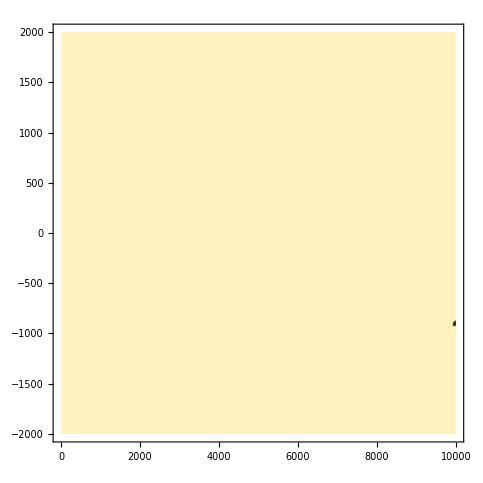

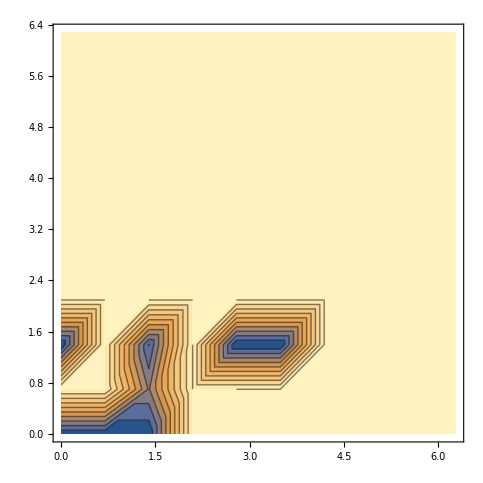

```mathematica
BinPosMin=Bin[PosMin[[1]],PosMin[[2]],PosMin[[3]],PosMin[[4]]];
ListContourPlot[Log[Chi2Hist[[All,All,BinPosMin[[3]],BinPosMin[[4]]]]],PlotRange->All,Contours->Log[{3.53,8.02,14.2}],DataRange->{{1,10000},{Mintb,Maxtb}}]
ListContourPlot[Chi2Hist[[BinPosMin[[1]],BinPosMin[[2]],All,All]],PlotRange->All,DataRange->{{0,2Pi},{0,2Pi}}]
```

```mathematica
N[Log[{3,10,100}]]
```

{1.09861,2.30259,4.60517}

```mathematica
Integrate[ChiSquareDistribution[2]]
```

Integrate::argmu: Integrate called with 1 argument; 2 or more arguments are expected.

Integrate[ChiSquareDistribution[2]]

```mathematica
NIntegrate[PDF[ChiSquareDistribution[2],x],{x,0,11}]
```

0.995913

```mathematica
Log[{3.53,8.02,14.2}]
```

{1.2613,2.08194,2.65324}

```mathematica
1.57043*180/Pi
```

89.979

```mathematica
ListContourPlot[Chi2Hist[[BinPosMin[[1]],BinPosMin[[2]],All,All]]]
```

ListContourPlot::gmat: (1.×10^6) is not a rectangular array larger than 2 x 2.

ListContourPlot[(1000000)]

```mathematica
Chi2Hist[[BinPosMin[[1]],BinPosMin[[2]],All,All]]
```

(1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000
1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000 | 1000000)